## §1. Import and Explore Data

### 1.1 Import Data

Import data from the disk files and set up vectors of independent and dependent variables, variable names, etc.

```mathematica
obs=Transpose[Import["observations.csv"]];
spend=Import["spend_values.csv"];
```

```mathematica
spendDollars=spend⟦2⟧;
obsNames=First/@obs;
obsData=Rest/@obs;
dependentVars=obsData⟦1⟧;
independentVars=obsData⟦2;;-1⟧;
```

### 1.2 Explore Data

#### Time Series Plots of Spend, Sales and Impressions

Spend dollars vary almost 10-fold across tactics.

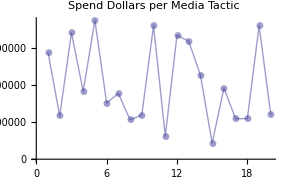

```mathematica
ListPlot[spendDollars, Joined->True, AxesOrigin->{0,0}, PlotLabel-> "Spend Dollars per Media Tactic",PlotStyle->{{Opacity[0.5], Thick}},PlotMarkers->Automatic]//Panel
```

There is no visually obvious seasonality pattern.  See checks for yearly seasonality below.

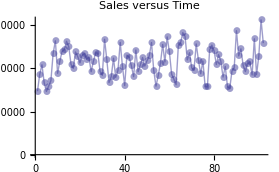

```mathematica
ListPlot[obsData⟦1⟧, Joined->True, PlotStyle->{{Opacity[0.5], Thick}},PlotMarkers->Automatic, PlotLabel->"Sales versus Time"]//Panel
```

There are no obvious relationships or features seen in the media impressions per tactic.

```mathematica
lines1={Thick,Hue[Random[]]//Darker,Line[#]}&/@Table[{i,j,obsData⟦i,j⟧},{i,2,21},{j,1,102}];
```

```mathematica
Graphics3D[lines1, Axes->True, BoxRatios->{3,2,0.15}, Boxed->False, AxesLabel->{"Media Tactic","Time","Impressions"}, ImageSize->550]//Panel
```

-Graphics3D-

Total impressions per media tactic are about the same across tactics.

```mathematica
impressionTotals=Total/@obsData⟦2;;21⟧;
```

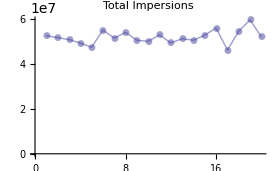

```mathematica
ListPlot[impressionTotals, Joined->True, PlotStyle->{{Opacity[0.5], Thick}},PlotMarkers->Automatic, PlotLabel->"Total Impersions", AxesOrigin->{0,0}]//Panel
```

The cost per impression does vary widely (about 10-fold) across tactics.

```mathematica
costPerImpression=spendDollars/impressionTotals;
```

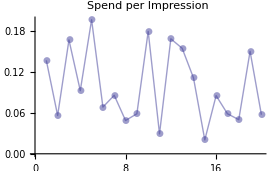

```mathematica
ListPlot[costPerImpression, Joined->True, PlotStyle->{{Opacity[0.5], Thick}},PlotMarkers->Automatic, PlotLabel->"Spend per Impression"]//Panel
```

#### Check for Seasonality

Checking correlations for both Correlating weeks [1-51] with [52-102] :

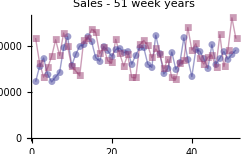
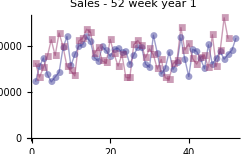

```mathematica
Row[{ListPlot[{obsData⟦1,1;;51⟧,obsData⟦1,52;;102⟧},Joined->True, PlotStyle->{{Opacity[0.5], Thick}},PlotMarkers->Automatic, PlotLabel->"Sales - 51 week years", ImageSize->250]//Panel,Spacer[30],ListPlot[{obsData⟦1,1;;52⟧,obsData⟦1,53;;102⟧},Joined->True, PlotStyle->{{Opacity[0.5], Thick}},PlotMarkers->Automatic, PlotLabel->"Sales - 52 week year 1",ImageSize->250]//Panel}]//Panel
```

Under either definition of the “year” (51 week or 52 week) the measured correlations fail to achieve significance

```mathematica
Correlation[obsData⟦1,1;;51⟧,obsData⟦1,52;;102⟧]//N
```

0.213774

... corresponding to a p=0.0661

```mathematica
Correlation[obsData⟦1,1;;50⟧,obsData⟦1,53;;102⟧]//N
```

0.135294

... corresponding to a p = 0.172

#### Check that the media tactic vectors are independent

If the media tactic vectors are linearly dependent, then the accuracy of distinguishing between their effects will be compromised. Looking their pairwise correlations, this should not be an issue here.

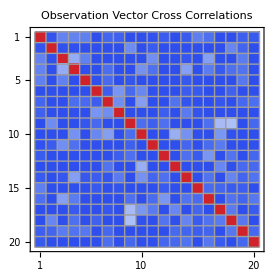
-Graphics--Graphics-

```mathematica
corrArray=ArrayPlot[Table[Correlation[obsData⟦i⟧,obsData⟦j⟧]//N,{i,2,21},{j,2,21}], ColorFunction->ColorData["TemperatureMap"], ColorFunctionScaling->False,Mesh->True,Frame->True,FrameTicks->All, ImageSize->400, PlotLabel->"Observation Vector Cross Correlations"];
colorScale=DensityPlot[y,{x,0,0.167},{y,0,1},ColorFunction->ColorData["TemperatureMap"], AspectRatio->Automatic, Frame->{False,True,False,False},ImageSize->70, PlotLabel->"Color Scale"];
Row[{corrArray,Spacer[50],colorScale}]//Panel
```

#### Are any tactics or structural features highly correlated with Sales a priori?

A few tactics and structural occurrences stand out a priori as possibly significant drivers.

```mathematica
corrCheck=Table[{i, obsNames⟦i⟧, Correlation[obsData⟦i⟧,obsData⟦1⟧]//N},{i,2,Length[obsNames]}];
SortBy[corrCheck,Last]//Reverse//TableForm
```

22 | Structural 1 Occurrence | 0.444081
15 | Media 14 Impressions | 0.387762
26 | Structural 5 Occurrence | 0.382494
10 | Media 9 Impressions | 0.377302
23 | Structural 2 Occurrence | 0.353122
5 | Media 4 Impressions | 0.296345
28 | Structural 7 Occurrence | 0.217397
17 | Media 16 Impressions | 0.185759
31 | Structural 10 Occurrence | 0.176143
19 | Media 18 Impressions | 0.173371
30 | Structural 9 Occurrence | 0.156756
12 | Media 11 Impressions | 0.146257
13 | Media 12 Impressions | 0.145653
2 | Media 1 Impressions | 0.14536
21 | Media 20 Impressions | 0.129229
3 | Media 2 Impressions | 0.109462
20 | Media 19 Impressions | 0.0943759
18 | Media 17 Impressions | 0.0853806
6 | Media 5 Impressions | 0.0689264
11 | Media 10 Impressions | 0.0580072
4 | Media 3 Impressions | 0.0574114
9 | Media 8 Impressions | 0.0487966
8 | Media 7 Impressions | 0.035643
7 | Media 6 Impressions | 0.0116358
24 | Structural 3 Occurrence | -0.0102375
14 | Media 13 Impressions | -0.0239564
16 | Media 15 Impressions | -0.0575986
29 | Structural 8 Occurrence | -0.132101
25 | Structural 4 Occurrence | -0.146671
27 | Structural 6 Occurrence | -0.25774

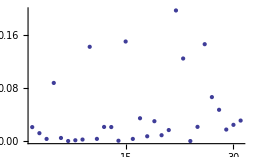

```mathematica
ListPlot[{#⟦1⟧,(#⟦3⟧)^2}&/@corrCheck, PlotStyle->PointSize[Large], PlotRange->All, AxesOrigin->{0,0}]
```

## §2. Modeling Strategy

The goal is to find a model which facilitates optimization of the marketing budget. To reduce the complexity of optimization, the final model should only contain those factors discovered to have been significant, i.e. the effective media tactics. Moreover, while modelling the return on investment for a media tactic as linear can give some insight on improving the budget, a more meaningful model must also capture the diminishing returns on each effective media tactic’s spend. Without a concept of diminishing returns, the optimal solution would be to spend the entire budget on the most effective tactic (in the absence of other constraints being applied).  

 The modeling approach followed these steps:
	1.  used a linear regression (lm1) to determine the relative impact and significance of media tactics and structural occurrences
	2. given the high significance of some structural factors, controlled for their impact by creating a synthetic dataset with the influence of structural factors removed;
	3. fitted a second linear model (lm2) with media tactics only (no structural occurrences)  to the synthetic dataset to ensure that the same factors found to be significant in part 2;
	4. sought a model which would facilitate optimization of the budget by capturing diminishing returns  - so far this remains an incomplete challenge.

### 2.1. Model 1 (lm1) - Media Tactics and Structural Occurrences

#### Fit Model

Fit a linear model with a constant term. 

A vectors of 1’s is added to the independent variables matrix, to represent the constant term.

```mathematica
independentVars2=Prepend[independentVars, Table[1,{i,1,Length[independentVars⟦1⟧]}]];
lm1=LinearModelFit[{independentVars2ᵀ,dependentVars}];
```

```mathematica
Panel[lm1ParamTab=lm1["ParameterTable"],"Parameter Information for Model lm1"]
```

| Estimate | Standard Error | t-Statistic | P-Value
#1 | 2.3704×10^6 | 354397. | 6.68853 | 4.35189×10^-9
#2 | 0.296073 | 0.149662 | 1.97828 | 0.0517783
#3 | 0.1364 | 0.159314 | 0.856167 | 0.394786
#4 | 0.205933 | 0.170872 | 1.20519 | 0.232131
#5 | 0.636391 | 0.159979 | 3.97798 | 0.0001655
#6 | -0.0306667 | 0.154136 | -0.198959 | 0.842863
#7 | -0.184728 | 0.147986 | -1.24828 | 0.216029
#8 | -0.220501 | 0.160316 | -1.37541 | 0.173329
#9 | 0.382436 | 0.1479 | 2.58578 | 0.0117686
#10 | 0.663702 | 0.152312 | 4.35753 | 0.0000435266
#11 | -0.0646519 | 0.165147 | -0.391482 | 0.696614
#12 | 0.471298 | 0.145034 | 3.24958 | 0.00176776
#13 | 0.285881 | 0.156126 | 1.83108 | 0.0712838
#14 | 0.199029 | 0.150349 | 1.32378 | 0.189824
#15 | 0.534845 | 0.147414 | 3.62818 | 0.000534183
#16 | 0.361451 | 0.145528 | 2.48372 | 0.0153639
#17 | 0.246715 | 0.153192 | 1.6105 | 0.111727
#18 | 0.141117 | 0.175906 | 0.802232 | 0.425096
#19 | 0.244333 | 0.143284 | 1.70524 | 0.0925216
#20 | 0.323353 | 0.144419 | 2.239 | 0.028291
#21 | 0.25253 | 0.149923 | 1.68439 | 0.0964972
#22 | 1.12752×10^6 | 126518. | 8.91195 | 3.41443×10^-13
#23 | 507246. | 104406. | 4.85841 | 6.83465×10^-6
#24 | 228916. | 114658. | 1.99652 | 0.0497128
#25 | 11461.6 | 147806. | 0.0775447 | 0.938408
#26 | 814693. | 114134. | 7.13806 | 6.55129×10^-10
#27 | -387759. | 123626. | -3.13656 | 0.00248785
#28 | 723990. | 127538. | 5.67667 | 2.7905×10^-7
#29 | -33411.9 | 106865. | -0.312654 | 0.75546
#30 | -48071.9 | 141154. | -0.340564 | 0.734438
#31 | 365966. | 133478. | 2.74176 | 0.00772725Parameter Information for Model lm1

```mathematica
lm1Results=lm1["ParameterTableEntries"];
```

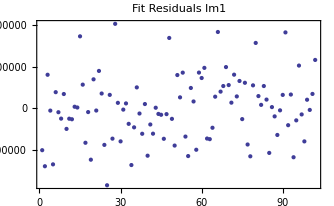

```mathematica
ListPlot[lm1["FitResiduals"],Frame->True,PlotRange->All, PlotLabel->"Fit Residuals lm1"]//Panel
```

```mathematica
lm1["RSquared"]
```

0.869017

```mathematica
lm1["AdjustedRSquared"]
```

0.813672

Visual check of model fit to dependent variables:

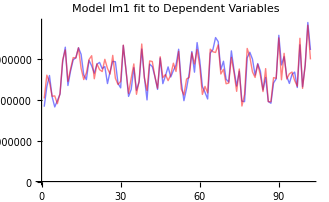

```mathematica
ListPlot[{obsData⟦1⟧,lm1@@@(independentVars2ᵀ)}, Joined->True, PlotStyle->{{Blue,Opacity[0.5], Thick},{Red,Opacity[0.5], Thick},{Green,Opacity[0.5], Thick}}, PlotLabel->"Model lm1 fit to Dependent Variables"]//Panel
```

#### Visualize results

Save the p-values and coefficients of the effects.

```mathematica
mediaResultsLm1=lm1Results⟦2;;21⟧;
structuralResultsLm1=lm1Results⟦22;;31⟧;
```

Transform p-values for plotting.

```mathematica
mediaResultsLm1Plot={#⟦1⟧,-Log[10,#⟦4⟧]}&/@mediaResultsLm1;
structuralResultsLm1Plot={#⟦1⟧,-Log[10,#⟦4⟧]}&/@structuralResultsLm1;
```

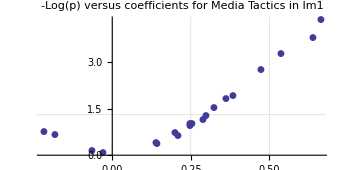

```mathematica
ListPlot[mediaResultsLm1Plot,
 Joined->False, PlotLabel->"-Log(p) versus coefficients for Media Tactics in lm1", PlotRange->All, AspectRatio->0.5, PlotMarkers->Automatic, GridLines->{Automatic,{-Log[10,0.05],5,10,15}}]//Panel
```

Visualize along with spend dollars for the tactic:

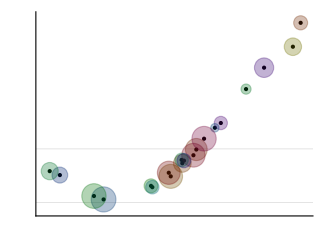
-Graphics--Log(p) versus coefficients for Media Tactics in lm1

```mathematica
gScale=7;sScale=0.7*10^5;
gPts=Graphics[Point[{#⟦1⟧,#⟦2⟧/gScale}]&/@mediaResultsLm1Plot, Axes->True];
gCircs=Graphics[{EdgeForm[Directive[Thin, Opacity[0.3]]],Hue[Random[]]//Darker//Darker,Opacity[0.3],Disk[{#⟦1⟧,#⟦2⟧/gScale},#⟦3⟧]}&/@Transpose[Append[mediaResultsLm1Plotᵀ,√spendDollars/(sScale)]]];
Panel[Show[gPts,gCircs, GridLines->{None,{{0,{Black,Thick}},{-Log[10,0.05]/gScale,{Thick,Dashed}}}},AxesStyle->Thick, Ticks->{None, None}],"-Log(p) versus coefficients for Media Tactics in lm1"]
```

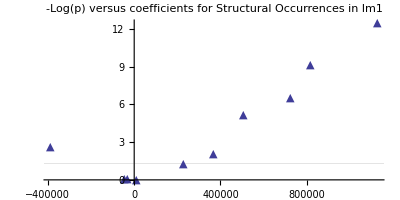

```mathematica
gStructPts=ListPlot[{#⟦1⟧,#⟦2⟧}&/@structuralResultsLm1Plot, Axes->True, AspectRatio->0.5, PlotMarkers->{▲,Large}, PlotLabel->"-Log(p) versus coefficients for Structural Occurrences in lm1"];
Show[gStructPts,GridLines->{{{0,{Black,Thick}}},{{0,{Black,Thick}},{-Log[10,0.05],{Thick,Dashed}}}}]//Panel
```

#### Select significant factors 1

```mathematica
mediaResultsLm1Labeled=Transpose[Prepend[mediaResultsLm1ᵀ,Table[i,{i,1,20}]]];
```

```mathematica
structuralResultsLm1Labeled=Transpose[Prepend[structuralResultsLm1ᵀ,Table[i,{i,21,30}]]];
```

```mathematica
significantMediaLm1=Select[mediaResultsLm1Labeled,(#⟦-1⟧<0.05)&];
```

```mathematica
significantStructuralLm1=Select[structuralResultsLm1Labeled,(#⟦-1⟧<0.05)&];
```

#### Quantify sales contribution from tactics

```mathematica
significantMediaCoeffsLm1=#⟦2⟧&/@significantMediaLm1
```

{0.636391,0.382436,0.663702,0.471298,0.534845,0.361451,0.323353}

```mathematica
significantMediaSignalsLm1 = significantMediaCoeffsLm1*Table[independentVars[[k]], {k, First /@ significantMediaLm1}];
```

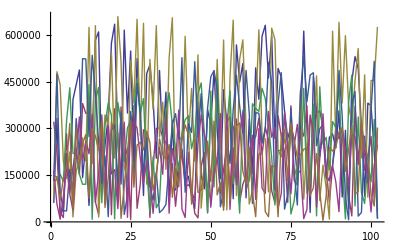

```mathematica
ListPlot[significantMediaSignalsLm1, Joined->True]
```

```mathematica
totalStructalMediaSignalsLm1 = Total[significantMediaSignalsLm1];
```

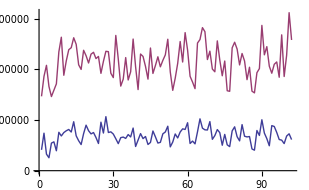

```mathematica
ListPlot[{totalStructalMediaSignalsLm1, dependentVars}, Joined -> True]
```

```mathematica
mediaTacticTotals=Total/@significantMediaSignalsLm1
```

{3.13136×10^7,2.06201×10^7,3.34884×10^7,2.489×10^7,2.69903×10^7,1.90518×10^7,1.92542×10^7}

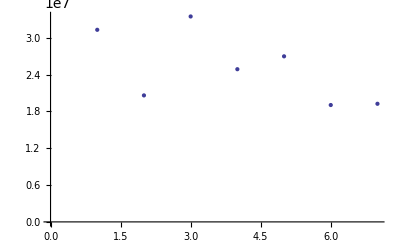

```mathematica
ListPlot[mediaTacticTotals, AxesOrigin->{0,0}]
```

```mathematica
significantMediaLm1
```

{{4,0.636391,0.159979,3.97798,0.0001655},{8,0.382436,0.1479,2.58578,0.0117686},{9,0.663702,0.152312,4.35753,0.0000435266},{11,0.471298,0.145034,3.24958,0.00176776},{14,0.534845,0.147414,3.62818,0.000534183},{15,0.361451,0.145528,2.48372,0.0153639},{19,0.323353,0.144419,2.239,0.028291}}

```mathematica
Transpose[{First/@significantMediaLm1,mediaTacticTotals/Total[dependentVars]}]
```

```mathematica
{{4,0.05718743867815046},{8,0.037658139954699216},{9,0.06115919113354672},{11,0.045456035437957405},{14,0.04929188737292361},{15,0.03479391859096084},{19,0.03516357155459409}}//TableForm
```

4 | 0.0571874
8 | 0.0376581
9 | 0.0611592
11 | 0.045456
14 | 0.0492919
15 | 0.0347939
19 | 0.0351636

```mathematica
Total[mediaTacticTotals/Total[dependentVars]]
```

0.32071

```mathematica
mediaTacticCosts=spendDollars⟦First/@significantMediaLm1⟧;
```

```mathematica
mediaTacticEfficiency=mediaTacticTotals/mediaTacticCosts;
```

```mathematica
Panel[Transpose[{First/@significantMediaLm1,mediaTacticEfficiency}]//TableForm,"Sales contribution of Media Tactics"]
```

4 | 6.85752
8 | 7.81717
9 | 11.2865
11 | 16.0782
14 | 4.79219
15 | 17.7198
19 | 2.14787Sales contribution of Media Tactics

```mathematica
costofEffectiveTactics=Total[mediaTacticCosts]
```

2.73909×10^7

```mathematica
percentEffectiveSpend=costofEffectiveTactics/Total[spendDollars]
```

0.26873

### 2.2. Remove the Effect of Structural Occurrences from the Dependent Variables (Sales)

```mathematica
significantStructuralCoeffsLm1=#⟦2⟧&/@significantStructuralLm1;
```

```mathematica
significantStructuralSignalsLm1 = significantStructuralCoeffsLm1*Table[independentVars[[k]], {k, First /@ significantStructuralLm1}];
```

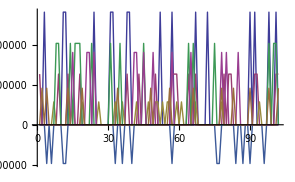

```mathematica
ListPlot[significantStructuralSignalsLm1, Joined -> True]
```

```mathematica
totalStructalSignalLm1 = Total[significantStructuralSignalsLm1];
```

```mathematica
salesLessStructLm1 = dependentVars - totalStructalSignalLm1;
```

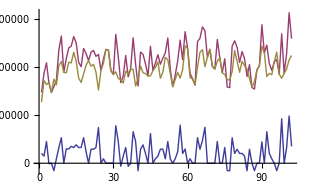

```mathematica
ListPlot[{totalStructalSignalLm1, dependentVars, salesLessStructLm1}, Joined -> True]
```

```mathematica
structuralTotals=Total/@significantStructuralSignalsLm1
```

{1.80403×10^7,9.63767×10^6,4.12048×10^6,1.30351×10^7,-5.42862×10^6,9.41187×10^6,4.75756×10^6}

```mathematica
Total[totalStructalSignalLm1]/Total[dependentVars]
```

0.0978418

```mathematica
Total[structuralTotals]/Total[dependentVars]
```

0.0978418

```mathematica
Panel[Transpose[{First/@significantStructuralLm1,structuralTotals/Total[dependentVars]}]//TableForm,"Sales Impact of Structural Occurrences"]
```

21 | 0.0329467
22 | 0.0176011
23 | 0.00752516
25 | 0.0238057
26 | -0.00991418
27 | 0.0171887
30 | 0.00868864Sales Impact of Structural Occurrences

### 2.3. Model 2 (lm2) - Modelling Media Tactics with Structural Occurrences Removed

Refit a linear model to establish that the selection and coefficients of significant effects are robust to the removal of the structural effects. We find the results are indeed robust, with good agreement between the significance results and the coefficients across both models.

```mathematica
independentVarsMedia=independentVars⟦1;;20⟧;
```

```mathematica
independentVarslm2=Prepend[independentVarsMedia, Table[1,{i,1,Length[independentVars⟦1⟧]}]];
```

```mathematica
lm2=LinearModelFit[{independentVarslm2ᵀ,salesLessStructLm1}];
```

```mathematica
lm2ParamTab=lm2["ParameterTable"]//Panel
```

| Estimate | Standard Error | t-Statistic | P-Value
#1 | 2.34448×10^6 | 311214. | 7.53334 | 6.19475×10^-11
#2 | 0.298245 | 0.13564 | 2.1988 | 0.0307443
#3 | 0.143169 | 0.142194 | 1.00686 | 0.317002
#4 | 0.202951 | 0.157068 | 1.29213 | 0.199988
#5 | 0.629968 | 0.141802 | 4.44258 | 0.0000278957
#6 | -0.0300375 | 0.137398 | -0.218617 | 0.827498
#7 | -0.175016 | 0.127892 | -1.36847 | 0.174949
#8 | -0.21139 | 0.139378 | -1.51666 | 0.133245
#9 | 0.379385 | 0.132022 | 2.87365 | 0.00517994
#10 | 0.658406 | 0.134255 | 4.90416 | 4.75688×10^-6
#11 | -0.0692611 | 0.145884 | -0.474767 | 0.636231
#12 | 0.487212 | 0.128501 | 3.79149 | 0.00028709
#13 | 0.286012 | 0.13703 | 2.08721 | 0.0400127
#14 | 0.196892 | 0.13166 | 1.49546 | 0.138681
#15 | 0.53593 | 0.127639 | 4.19881 | 0.0000684032
#16 | 0.359922 | 0.124805 | 2.88386 | 0.00503028
#17 | 0.236051 | 0.134676 | 1.75273 | 0.0834325
#18 | 0.142425 | 0.15581 | 0.914099 | 0.363378
#19 | 0.248597 | 0.125982 | 1.97328 | 0.0518739
#20 | 0.329414 | 0.128324 | 2.56705 | 0.0120966
#21 | 0.25831 | 0.128597 | 2.00867 | 0.0479041

```mathematica
lm2Results=lm2["ParameterTableEntries"];
```

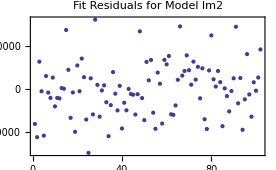

```mathematica
ListPlot[lm1["FitResiduals"],Frame->True,PlotRange->All, PlotLabel->"Fit Residuals for Model lm2"]//Panel
```

```mathematica
lm2["RSquared"]
```

0.699337

```mathematica
lm2["AdjustedRSquared"]
```

0.625099

Visual check of model fit to dependent variables:

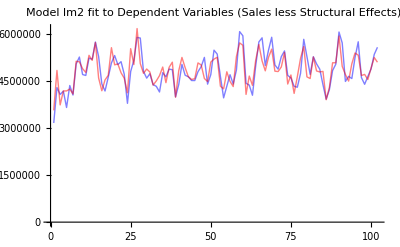

```mathematica
ListPlot[{salesLessStructLm1,lm2@@@(independentVarslm2ᵀ)}, Joined->True, PlotStyle->{{Blue,Opacity[0.5], Thick},{Red,Opacity[0.5], Thick},{Green,Opacity[0.5], Thick}}, PlotLabel->"Model lm2 fit to Dependent Variables (Sales less Structural Effects)"]//Panel
```

#### Compare results from lm1 and lm2

Scatter plots compare how well significance and coefficients match across models lm1 and lm2.

```mathematica
lm1Results//Length
```

31

```mathematica
lm2Results//Length
```

21

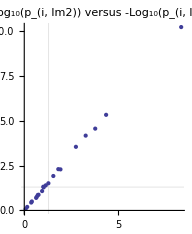

```mathematica
compareLm1Lm2PValues=Transpose[{-Log[10,#⟦-1⟧]&/@lm1Results⟦1;;21⟧,-Log[10,#⟦-1⟧]&/@lm2Results}];
ListPlot[compareLm1Lm2PValues, GridLines->{{{-Log[10,0.05],{Thick,Dashed}}},{{-Log[10,0.05],{Thick,Dashed}}}}, AspectRatio->Automatic, PlotLabel->"-Log_10(p_(i, lm2)) versus -Log_10(p_(i, lm1))"]//Panel
```

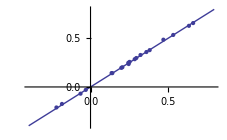

```mathematica
compareLm1Lm2Coeffs=Transpose[{#⟦1⟧&/@lm1Results⟦2;;21⟧,#⟦1⟧&/@lm2Results⟦2;;-1⟧}];
lnPlot1=Plot[x,{x,-0.4,0.8}];
lpPlot1=ListPlot[compareLm1Lm2Coeffs, AspectRatio->Automatic, PlotRange->All,PlotLabel->"Coefficients for lm2 versus for lm1"];
Show[lnPlot1,lpPlot1]//Panel
```

### 2.4. Incomplete - Model 3 (lm3) - Modelling Media Tactics with Structural Occurrences Removed, Quadratic Terms Included

As noted in the strategy above, numerical optimization of the budget would be more meaningful if we can model the extent to which the benefits realized from a media tactic (in terms of increased sales) exhibit diminishing returns with increased investment in that tactic. To that end, quadratic or other nonlinear terms must be introduced so as to ascertain information about the rate of change of effectiveness - roughly speaking, how the coefficients discovered above change as spending on the tactic varies.

We select the observation vectors associated with the 7 media tactics found to be effective:

```mathematica
sigMediaIndependentVars=independentVarsMedia⟦#⟦1⟧&/@significantMediaLm1⟧;
```

```mathematica
dataLm3=(Append[sigMediaIndependentVars,salesLessStructLm1 ])ᵀ;
```

Define a model with a constant term, and both linear and quadratic terms in seven variables

```mathematica
modelLm3=c0+a1 x1+b1 x1^2+a2 x2+b2 x2^2+a3 x3+b3 x3^2+a4 x4+b4 x4^2+a5 x5+b5 x5^2+a6 x6+b6 x6^2+a7 x7+b7 x7^2;
paramsLm3={c0,a1, a2,a3,a4,a5,a6,a7,b1,b2,b3,b4,b5,b6,b7};
varsLm3={x1,x2,x3,x4,x5,x6,x7};
```

```mathematica
scaleFactor=1000000;
lm3=NonlinearModelFit[dataLm3/scaleFactor, modelLm3,paramsLm3,varsLm3];
```

Note that very few of the parameters here have high significance and the poor t-statistics are also low: there is no reason to believe that this is a good model for the data

```mathematica
lm3ParamTab=lm3["ParameterTable"]//Panel
```

| Estimate | Standard Error | t-Statistic | P-Value
c0 | 3.13878 | 0.35947 | 8.73169 | 1.59114×10^-13
a1 | -0.388901 | 0.57763 | -0.67327 | 0.50256
a2 | 0.920866 | 0.598205 | 1.53938 | 0.12734
a3 | 1.31995 | 0.607013 | 2.1745 | 0.0323816
a4 | -0.0248982 | 0.622284 | -0.040011 | 0.968176
a5 | 0.158383 | 0.552293 | 0.286773 | 0.774968
a6 | 0.0165584 | 0.580098 | 0.0285441 | 0.977294
a7 | 0.647819 | 0.64594 | 1.00291 | 0.318686
b1 | 1.10258 | 0.560289 | 1.96787 | 0.0522681
b2 | -0.671907 | 0.576389 | -1.16572 | 0.246914
b3 | -0.532171 | 0.566213 | -0.939878 | 0.349883
b4 | 0.534588 | 0.604775 | 0.883945 | 0.379162
b5 | 0.451717 | 0.533213 | 0.847161 | 0.39923
b6 | 0.396585 | 0.55132 | 0.719337 | 0.473861
b7 | -0.223722 | 0.573905 | -0.389824 | 0.697619

The fitting may be numerically unstable, the data may not support the hypothesis of diminishing retrains or the quadratic form may not be a good description of the dependent variable’s behavior.